#### Arithmetic

Shift+Enter, Exact v. approximate, caps

```mathematica
N[{E,I,Pi}]
```

#### Naming constants

```mathematica
a=5;
a^2+a
```

#### Solving and replacements

space for multiplication, double equal for equality,

```mathematica
soln=Solve[x^2-12x+4==0,x]
```

{{x→2 (3-2 √2)},{x→2 (3+2 √2)}}

#### Most common mistakes

```mathematica
solve(a x^2+bx+c=0)
```

Brackets, braces, parens.
Caps, spelling.
Space for multiplication.
Double equal for equations.
Clear previous definitions.  Conversely, be sure to (re)-execute definitions you want.

#### Plotting and options

Caps, square brackets, iterators, options, annotation, color coding.

#### Defining functions

Factorial, fib.

#### Patterns

Collatz function.

#### Creating and manipulating lists.

Table, NestList, Map, Select, Take, Part, Flatten

#### Getting help

?*Q*
www.wolfram.com/learningcenter/

### Example problems

Execute or re-execute--watch for echo back.
Supply all arguments, know what you want to do mathematically.
Build up calculations slowly.

#### Perfect numbers.

Clear, define, test in same cell.

```mathematica
Clear[pq]
rep[{p_,n_}]:=p n
pq[x_]:=Total[Divisors[x]]==2x
Select[Range[1000000],pq]
```

{6,28,496,8128}

#### Birthday paradox

#### Module

#### FindRoot, DSolve, Fit, Interpolation

#### Queue

```mathematica
Manipulate[
Module[{stime,atime,f},
stime[]:=RandomReal[{1,a}];
atime[]:=RandomReal[{0,b}];
f[{t_,0,s_,a_}]:={t+a,1,stime[],atime[]};
f[{t_,w_,s_,a_}]:={t+s,w-1,stime[],a-s}/;s<a;
f[{t_,w_,s_,a_}]:={t+a,w+1,s-a,atime[]}/;a≤s;
ListLinePlot[Take[#,2]&/@NestList[f,{0,0,0,0},n]]
],
{a,1,5},{b,1,5},{n,1,10000,1}
]
```

#### Predator Prey

```mathematica
ⅆx/ⅆt == x (1-x) - (a x y)/(x+b)
ⅆy/ⅆt == c y (1-y/x)
```

```mathematica
Manipulate[
soln=NDSolve[{x'[t]==x[t](1-x[t])-a x[t] y[t]/(x[t]+b),y'[t]==c y[t](1-y[t]/x[t]),
x[0]==1,y[0]==1},{x[t],y[t]},{t,0,500}];
Plot[{x[t],y[t]}/.soln,{t,0,500},PlotRange->All],
{a,0,2},{b,0,2},{c,0,2}
]
```

NDSolve::ndsz: At t == 1.6797, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 0.706775, step size is effectively zero; singularity or stiff system suspected.

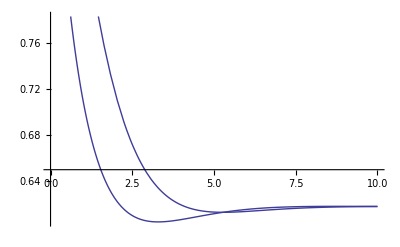

```mathematica
Plot[{x[t],y[t]}/.soln,{t,0,10}]
```

```mathematica
Plot[{x[t],y[t]}/.,
{t,0,100}
]
```

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00204286 cannot be used as a variable.

ReplaceAll::reps: {« 1 »} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 2.04286 cannot be used as a variable.

General::stop: Further output of NDSolve will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll will be suppressed during this calculation.

-Graphics-

```mathematica
Manipulate[
eqns={B'[t]==a (10-B[t])-b L[t],L'[t]==c (1+L[t])B[t]+d S[t]B[t],S'[t]==e(6-S[t])L[t],B[0]==1,L[0]==1,S[0]==1};
s=NDSolve[eqns,{B[t],L[t],S[t]},{t,0,100}];
Plot[{B[t],L[t],S[t]}/.s[[1]],{t,0,100}],
{{a,1},-1,1},
{{b,1},-1,1},
{{c,1},-1,1},
{{d,1},-1,1},
{{e,1},-1,1},
{{f,1},-1,1},
{{g,1},-1,1},
{{h,1},-1,1}
]
```

NDSolve::ndsz: At t == 4.45437, step size is effectively zero; singularity or stiff system suspected.

### Additional

#### Manipulate

#### Graphics

#### Import, Export, Curated data

#### TeXForm

```mathematica
TeXForm[HoldForm[Integrate[x,{x,0,11}]]]
```

\int_0^{11} x \, dx